```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/big_brother/Documents/TaskDash/Boundary/explicit_finite_difference

```mathematica
fo = Import["exp_fo.txt","Table"][[12;;]];
xh = Import["exp_xh.txt","Table"][[12;;]];
```

```mathematica
fo = ({fo[[1]],fo[[#]]})ᵀ&/@Range[2,4];
xh =({xh[[1]],xh[[#]] })ᵀ&/@Range[2,4];
```

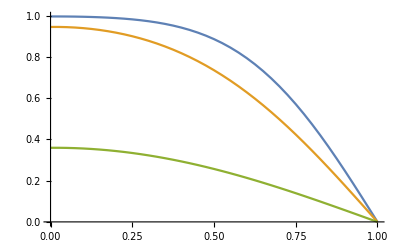

```mathematica
ListPlot[fo, Joined->True]
```

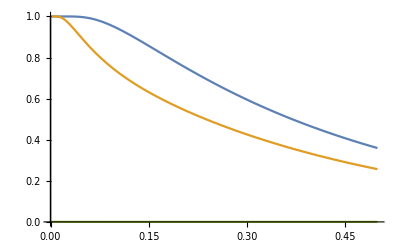

```mathematica
ListPlot[xh, Joined->True]
```

```mathematica
xh[[3]]
```

{{0.,1.},{0.00015625,0.000537892},{0.0003125,0.000403492},3194,{0.499531,7.69888×10^-6},{0.499688,7.69584×10^-6},{0.499844,7.69279×10^-6}}
 |  |  |  |